# Mathematica Tutorial 3 Programing with conditional statements

by C. Golé, Smith College © 2011, revised 2024.

## Introduction

When we want a program to do different things according to some conditions, we use conditional statements such as "If". As an example, in this rather useless program, we want to successively triple x if it is in the interval (2, 100) and halve it otherwise. Will the process converge?

```mathematica
x = 5;
Do[
If[x>2 && x<100 , (* if x > 2 and x < 100  *)
x = 3 x,  (* then triple x *)
x = .5 x  (* else halve x *)
];
Print[x],
{20}
]
```

15

45

135

67.5

202.5

101.25

50.625

151.875

75.9375

227.813

113.906

56.9531

170.859

85.4297

256.289

128.145

64.0723

192.217

96.1084

288.325

As you see, crucial in this program is the command If, in which a logical condition (x < 100 && x > 2) is tested. We first look at these testing expressions and then explore conditional statements.

## 1. If and Which (conditionals)

### Testing Expressions

Conditions are logical statements that can be True or False. Try this:

```mathematica
4<3
4<3 && 5>3   (* && is the logical And *)
4<3 || 5>3   (* || is the logical Or *)
4 == 2       (* == is the logical Equal *)
4 != 2       (* != is the logical Not equal *)
!(4<3) (* Guess what this does before you execute...)
```

False

False

True

False

True

There is much more (search testing expressions in the Help menu).

### If

Here is a silly command. Execute it and then change 3<4 to 3>4



```mathematica
If[3>4, Print["carrot"], Graphics[Disk[{0,0},1]]]
```

The general structure of the If command is
		If[Condition,  Then (do this if Condition is true) , Else (do that if false)]  .

The If command can be used to define piecewise functions

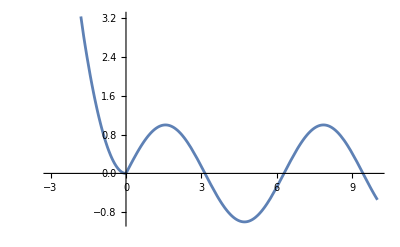

```mathematica
pieceFun[x_] := 
If[x>0, (* Condition *)
Sin[x], (* Then *)
 x^2   (* Else *)
];
Plot[pieceFun[x], {x, -3,10}]
```

#### QRQ 1.1 a. Define a piecewise function which is equal to x + 1 when x <2 and to - x when x ≥2 b. Search for other ways to define and plot piecewise functions in Mathematica. Show at least one other way to define and plot the function in a.

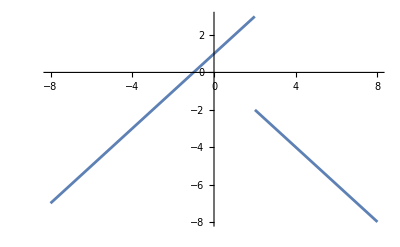

```mathematica
Plot[Piecewise[{{x+1, x<2},{-x,x>=2}}],{x,-8,8}]
```

If statements can be useful in loops as well (as seen in the program in the introduction above):

```mathematica
Do[
If[k < 5,    (* Condition *)
Print[2 k], (* Then *)
Print[-3 k]    (* Else *)
],
{k, 1, 10}
]
```

2

4

6

8

-15

-18

-21

-24

-27

-30

It is instructive to look at this program step by step, as k varies between 1 and 10, as if we were the computer:
Step k=1: as we enter the Do loop, k=1. Since the condition k < 5 is satisfied, we execute the first command, Print[2 k]
Steps k=2-4: same as Step 1
Step k=5: first step in the loop at which k is not < 5. So we start executing the second command, Print[-3k]
Steps k = 6- 10: k >5, so we continue with Print[-3 k]

#### QRQ 1.2 Look up the conditional EvenQ function and create a Do loop that runs for an index k between 2 and 12 and, at each step, prints k/2 when k is even, and (k+1)/2 when k is odd.

### Which

Some times you want to consider more than two alternatives. As example, here is a function which is defined in 3 pieces:

```mathematica
zigzag[x_]:=
Which[
x<-1, -2 - x, 
x>= -1 && x< 1, x,
x >= 1, 2-x
]
```

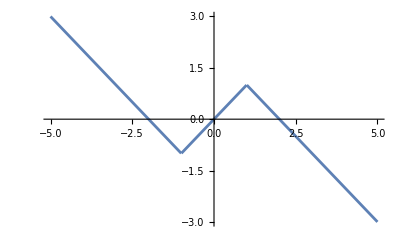

```mathematica
Plot[zigzag[x], {x, -5, 5}]
```

#### QRQ 1.3 Using Which, define a function that has the following graph (the middle piece is a parabola):

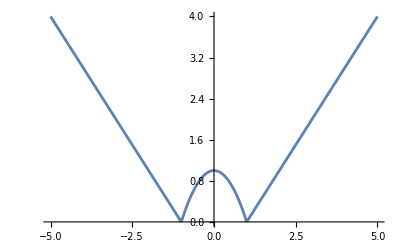

```mathematica
bigw[x_]:=
Which[
x<-1, -x-1, 
x>= -1 && x< 1, -x^2+1,
x >= 1,x-1
]
Plot[bigw[x], {x, -5, 5}]
```

As for "If", the command "which" can be used to write programs. An example is the Second Derivative Project (will be posted). To define piecewise functions, there is also the command Piecewise.

## 2 For-loops

For-loops are ubiquitous in programing. In Mathematica, they can substitute for Do-loops -  a matter of style - but they also have the versatility of While-loops that you may know from other programing languages.

Look at the following program, and try to guess what it will be doing at each step:

```mathematica
For[i = 0, (* initial value of index i *)
	i < 6, (* test *)
	i++, (* increment - equivalent to i = i+1 *)
	If[i<3, Print[i], Print[i/2]];
	]
```

0

1

2

3/2

2

5/2

Look up the general syntax:

```mathematica
?For
?Do
```

#### QRQ 2.1 Write a Do loop that does the same thing as the above For loop.

```mathematica
i=0
Do[If[i<3, Print[i], Print[i/2]], {i,0,5}]
```

0

0

1

2

3/2

2

5/2

So, why learn about For loops if they do the same thing as Do loops, and look more complicated? The trick is that the test can be more sophisticated than in the above loop, and can stop the program after an unknown number of steps, when the test is satisfied. Here is an example where we repeatedly double x with x starting with 3, until x is larger than 2000.

```mathematica
x = 3;
For[i = 0,  (* initial value of index i *)
	 i <  10000 && x < 2000, (* test *)
	i++, (* iterator - equivalent to i = i+1 *)
	x = 2 x;
       If[x<2000,Print[x]]
	]
```

6

12

24

48

96

192

384

768

1536

#### QRQ 2.2 Change this program in a minor way so the last output is really less than 2000.

Note: If you like to live dangerously, you can change the test i <  10000 && x < 2000 to just x < 2000.  While adding the condition  i <  10000  might slow things down a little, it is providing a safety net: When your program is complicated, your test might never be satisfied (especially if you made a mistake) and you might get yourself into an infinite loop. It will happen to you, as it does to every programmer, so we might as well make it happen now so that you can learn how to stop it. But first let's make sure you you have a parachute:
Before running this program, save your work, copy the program in a new file, and identify the menu command: Evaluation/Quit Kernel/local which you will need to interrupt. Then take the plunge... You can try to Command _. (Mac) or Control_. (Windows) and if it does not work, Evaluation/Quit Kernel/local.

```mathematica
For[i = 0, 3 < 200, i++, 
Print[i]
]
```

Note:  For those who have seen some programing before, For in Mathematica can act like a While. Mathematica also has a separate While command, but with For's expanded capability, we won't need While. For a While at least :-)

#### QRQ 2.3 a. Explain what this For Loop does, line by line, step by step, as in the example below QRQ1.1

```mathematica
j = 1;
k = 1;
m = 1;
Print[j]
Print[k] (*value check original vals.*)
For[i = 0, i < 14, i++, (*continue as long as i is less than 6. itterate each time*)
	j = k; (*assign value of k to j, so j=1, round 2, j=2*)
k = m;	(* reassign value of m to k.*)
m = k +j; (*adds value of k and j*)
	 
	Print[m]; (*print value of m*)
   ]
```

1

1

2

3

5

8

13

21

34

55

89

144

233

377

610

987

#### b. Change the order of 2 of the lines of the program so that it outputs the Fibonacci numbers 1 1 2 3 5 8 13.... (notice each one is the sum of the 2 previous ones: F_0=1, F_1=0, F_(n+1)=F_n+F_(n-1))

#### c. Change the program in b so that it prints all the Fibonacci numbers that are less than 10000

#### d. Turn this program into a function fibLessThan[n] which outputs the greatest Fibonacci number less than n.

```mathematica
Clear[i,j,k,m]

fibLessthan[n_]:={
j = 1;
	k = 0;
	m = 1;

For[i = 0, i < n, i++, 
	j = k; 
k = m;
m = k +j;
If[m <=n,Print[m]]]}

fibLessthan[89]
```

1

2

3

5

8

13

21

34

55

89

#### e. Click here to find out about Lucas numbers, and modify the function fibLessThan[n] to create a function lucas[n] which gives the greatest Lucas number less than n. f. Find at least three ways to produce the n^th Fibonacci number (With the convention that F_0=1, F_1=0). One of these ways should be a modification of b and/or d. For the other two ways, you have the right to cheat, using help menu or the web. In fact you should cheat here, but you should cite your sources.

```mathematica
Clear[i,j,k,m]

flucas[n_]:={
j = 0;
	k = 2;
	m = 1;
Print[m];
For[i = 0, i < n, i++, 
	j = k; 
k = m;
m = k +j;
If[m <=n,Print[m]]]}

flucas[89]
```

1

3

4

7

11

18

29

47

76

{Null}

### Interesting example of For-loop: finding the root of the equation cos(x) = x

For (or While) is often used when you want to get to a certain precision in a computation, and don't know how long it will take.
Careful, don't forget to use a bound on the number of steps (10 millions here).

```mathematica
x =1.0;
For[i=0, i<10000000 && Abs[x-Cos[x]]> 10^(-10), i++,
x = Cos[x];
]
NumberForm[x, 20]
x - Cos[x]
Clear[x]
```

0.7390851331706995

-7.44108×10^-11

Check graphically:

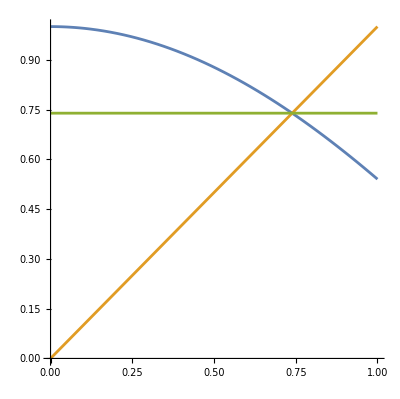

```mathematica
Plot[{Cos[x], x, 0.7390851331706995}, {x, 0,1}, AspectRatio-> Automatic]
```

Can you figure out graphically why the program  gives you the solution of x = cos(x)?
Or check it with one of Mathematica' s own equation solving command :

```mathematica
FindRoot[x==Cos[x], {x,1}] (* 1 is the starting guess *)
NumberForm[%[[1,2]], 20]
```

{x→0.739085}

0.7390851332151607